# How Target Configurations Affect the Optical Characteristics

## A Study of Linear Chain Aggregates, Densely Packed Clusters, Random Configurations, and Distinct Configurations

```mathematica
Grid[{{Style["Linear chain","Title"],Style["Packed cluster","Title"]},
{-Graphics3D-,-Graphics3D-},
{,}}]
```

Linear chain | Packed cluster
-Graphics3D- | -Graphics3D-
 |

# Phase Function (p(r̂,(n̂)^inc))

p(r̂,(n̂)^inc)=(4π)/C_sca dC_sca/dΩ

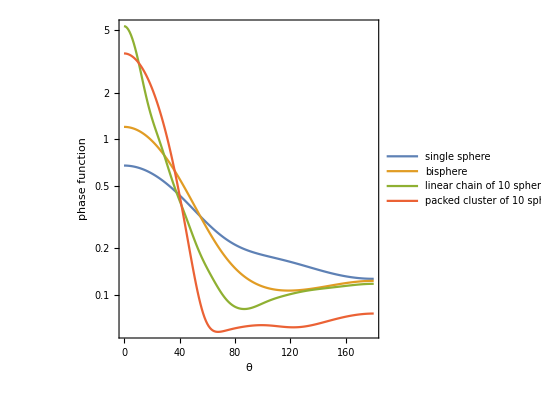

# Stokes Parameter (I)

I=(I
Q
U
V)=1/2 √(ε/μ)(E_(0ϑ)E_(0ϑ)^*+E_(0φ)E_(0φ)^*
E_(0ϑ)E_(0ϑ)^*-E_(0φ)E_(0φ)^*
-E_(0ϑ)E_(0φ)^*-E_(0φ)E_(0ϑ)^*
i(E_(0φ)E_(0ϑ)^*-E_(0ϑ)E_(0φ)^*))

-Graphics-

# Linear Polarization Degree (P_L)

P_L=-F_12/F_11

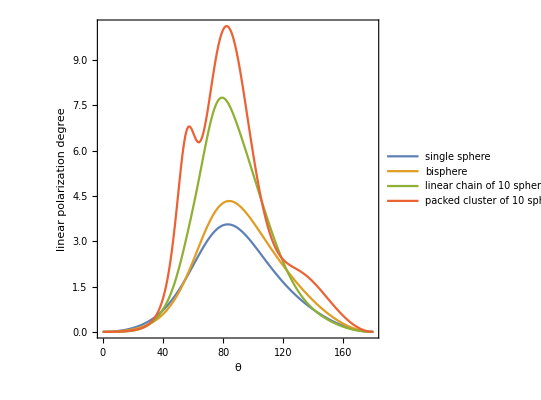

# Cross Section Efficiencies (Q_ext,Q_sca,Q_abs)

Q_ext=C_ext/G=W_ext/(1/2 G √(ε_1/μ_0)(|E_0^inc|)^2)
Q_sca=C_sca/G=W_sca/(1/2 G √(ε_1/μ_0)(|E_0^inc|)^2)
Q_abs=C_abs/G=(C_ext-C_sca)/G

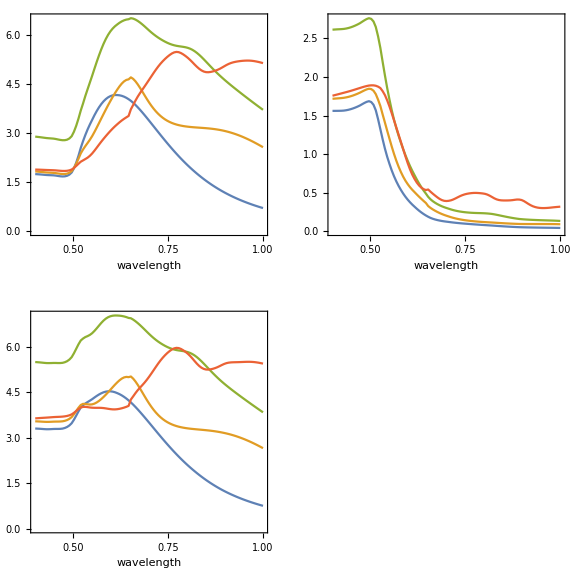
-Graphics-
top left to right:scattering cross section efficiency,absorption cross section efficiency
bottom left:extinction cross section efficiency

# Asymmetry Parameter (<cos Θ > )

<cos Θ > =1/C_sca∫_(4π) ⅆΩ dC_sca/dΩ r̂·(n̂)^inc

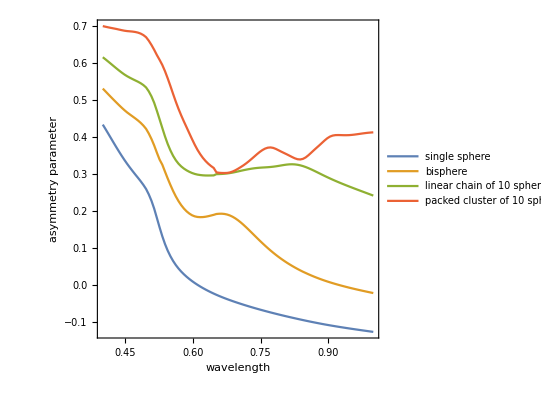

# Discussions

For phase functions and linear polarization degrees which are plotted against scattering angle, linear chain’s functions are more identical to bisphere’s and single sphere’s in both shapes and values rather than packed cluster’s functions.

For cross section efficiencies and asymmetry parameters which are plotted against wavelength, linear chain’s curves have more similar shapes with bisphere’s and single sphere’s rather than packed cluster’s curves do because packed cluster’s functions are wavier than the others.

We can conclude that linear chain aggregates have closer optical characteristics to bispheres and single spheres than densely packed clusters do.

Hypothetically, it is because in linear chain aggregates there are less multiple scattering occurrence as the particles are less in contact with each other than the particles in packed clusters

We can also conclude that the optical characteristic difference strongly depends on angular distributions, instead of wavelength or refractive index.

# Key Questions

Are the conclusions correct? Need more data.

Could we find the difference in the quantities that are more easily measured, e.g. in absorbance?

# Linear Chains

```mathematica
Grid[{{Style["10 spheres","Chapter"],Style["20 spheres","Chapter"],Style["30 spheres","Chapter"]},
{-Graphics3D-,-Graphics3D-,-Graphics3D-},
{,,}}]
```

10 spheres | 20 spheres | 30 spheres
-Graphics3D- | -Graphics3D- | -Graphics3D-
 |  |

# Packed Clusters

```mathematica
Grid[{{Style["10 spheres","Chapter"],Style["20 spheres","Chapter"],Style["30 spheres","Chapter"]},
{-Graphics3D-,-Graphics3D-,-Graphics3D-},
{,,}}]
```

10 spheres | 20 spheres | 30 spheres
-Graphics3D- | -Graphics3D- | -Graphics3D-
 |  |

# Phase Function (p(r̂,(n̂)^inc))

p(r̂,(n̂)^inc)=(4π)/C_sca dC_sca/dΩ

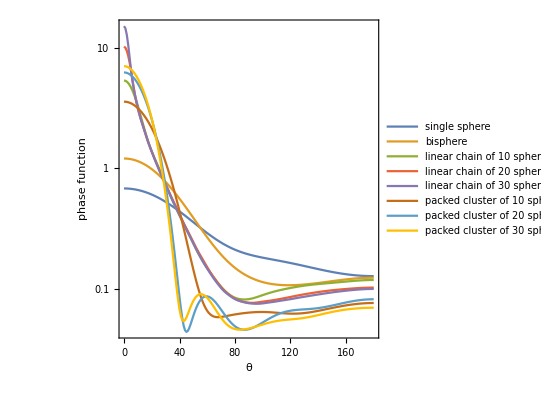

# Linear Polarization Degree (P_L)

P_L=-F_12/F_11

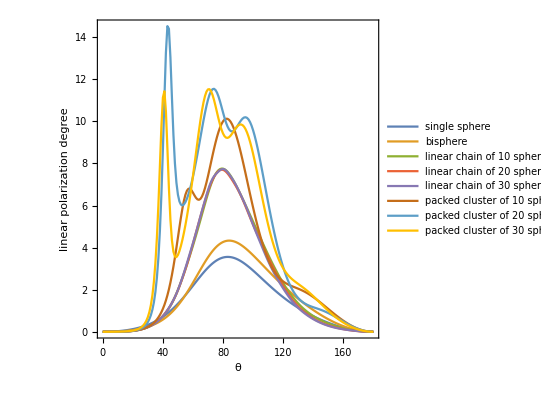

# Cross Section Efficiencies (Q_ext,Q_sca,Q_abs)

Q_ext=C_ext/G=W_ext/(1/2 G √(ε_1/μ_0)(|E_0^inc|)^2)
Q_sca=C_sca/G=W_sca/(1/2 G √(ε_1/μ_0)(|E_0^inc|)^2)
Q_abs=C_abs/G=(C_ext-C_sca)/G

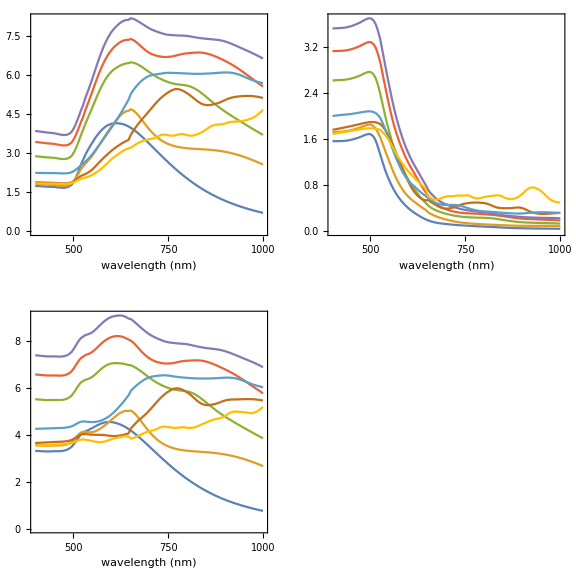
-Graphics-
top left to right:scattering cross section efficiency,absorption cross section efficiency
bottom left:extinction cross section efficiency

# Asymmetry Parameter (<cos Θ > )

<cos Θ > =1/C_sca∫_(4π) ⅆΩ dC_sca/dΩ r̂·(n̂)^inc

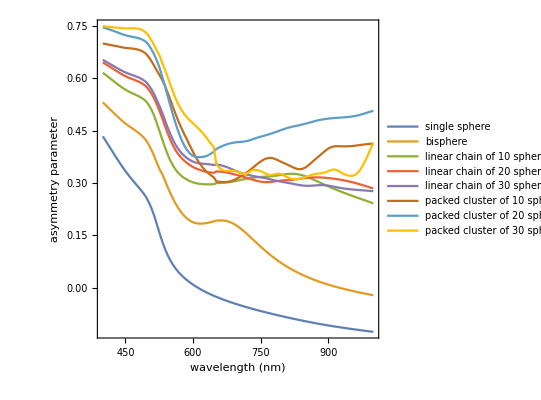

# Discussions for Key Question #1

Conclusions in the previous discussion remain valid even after we add more samples with varying sphere numbers.

In addition, aggregate configurations have greater influence on optical characteristics than particle numbers do, which is characterized by the same aggregate configuration’s functions with different sphere numbers having closer values to each other rather than the same sphere number configuration’s function with different aggregate configurations.

# Adapting Transmittance Concept in Simulations to the Experiments

-Graphics-

# Periodic Configurations (1/2)

## Cell dimensions = 3 × 3 μm^2

```mathematica
Grid[{{Style["Single spheres","Chapter"],Style["Horizontal bispheres","Chapter"],Style["Vertical bispheres","Chapter"]},
{-Graphics3D-,-Graphics3D-,-Graphics3D-},
{,,}}]
```

Single spheres | Horizontal bispheres | Vertical bispheres
-Graphics3D- | -Graphics3D- | -Graphics3D-
 |  |

# Periodic Configurations (2/2)

## Cell dimensions = 3 × 3 μm^2

```mathematica
Grid[{{Style["Horizontal linear chains","Chapter"],Style["Vertical linear chains","Chapter"],Style["Packed clusters","Chapter"]},
{-Graphics3D-,-Graphics3D-,-Graphics3D-},
{,,}}]
```

Horizontal linear chains | Vertical linear chains | Packed clusters
-Graphics3D- | -Graphics3D- | -Graphics3D-
 |  |

## Reflectance vs wavelength

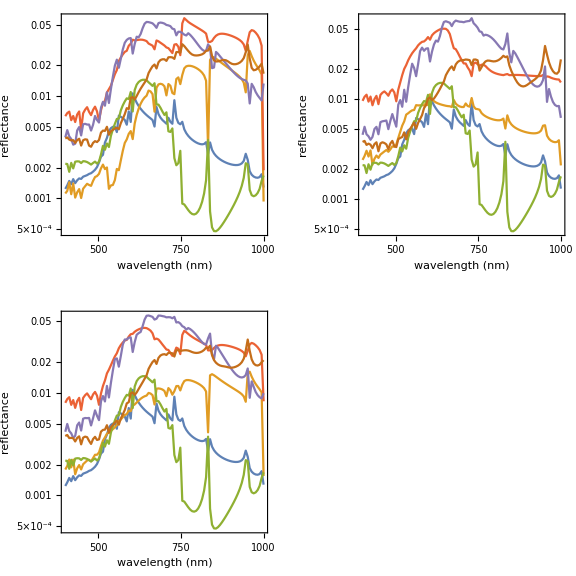
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorptance vs wavelength

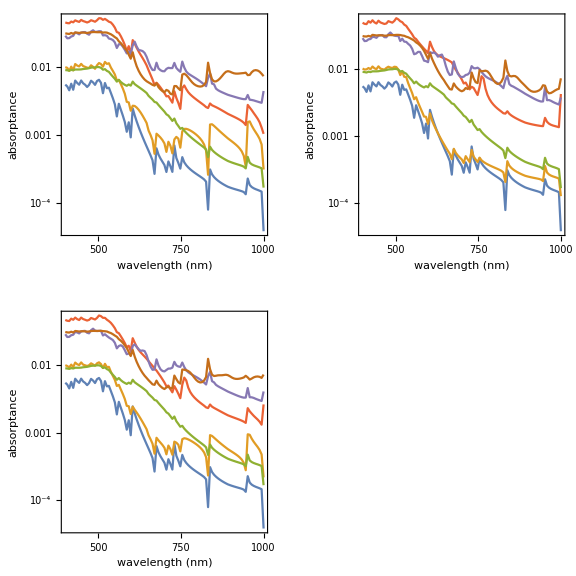
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Transmittance vs wavelength

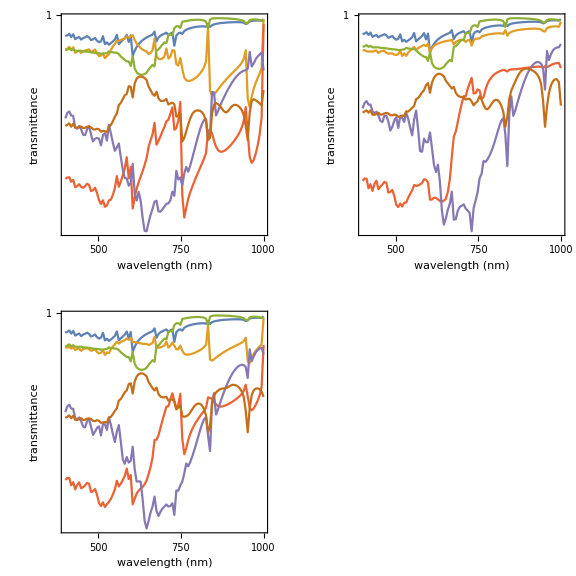
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorbance vs wavelength

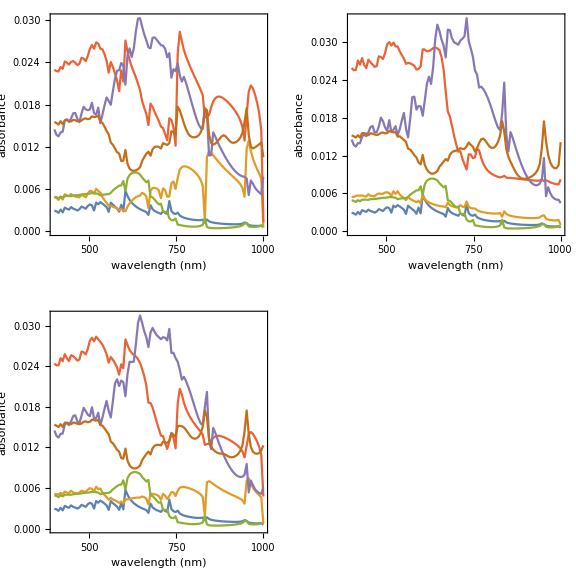
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Reflectance vs incident angle

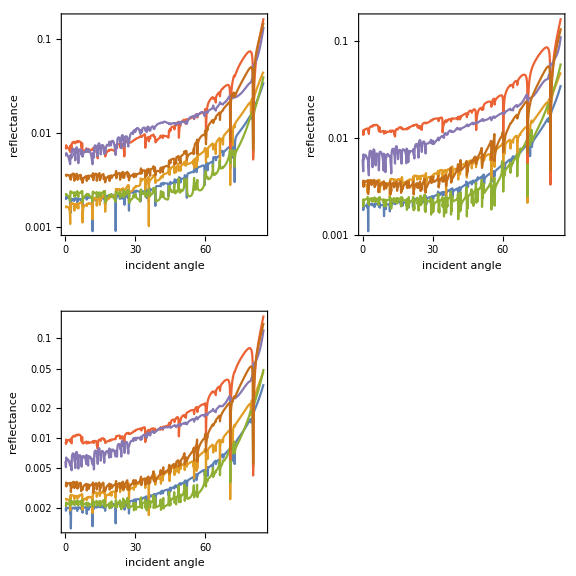
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorptance vs incident angle

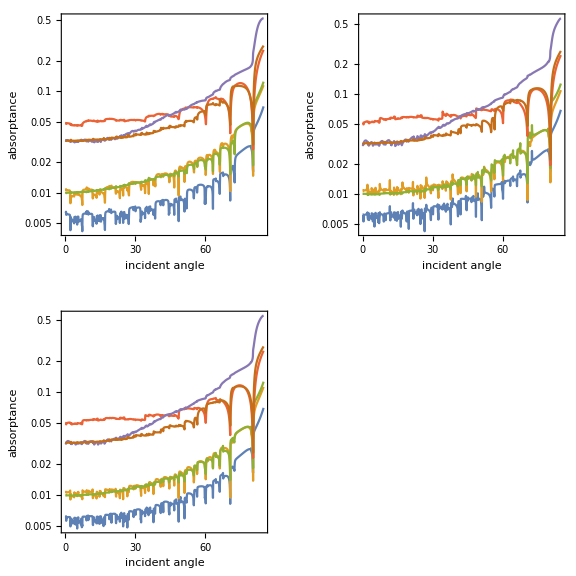
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Transmittance vs incident angle

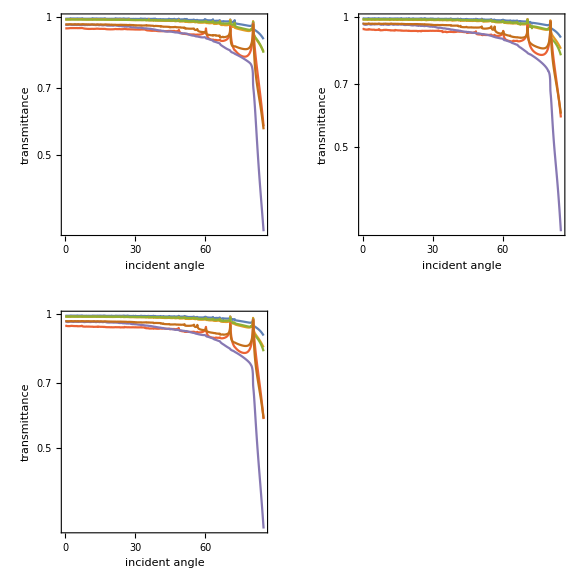
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorbance vs incident angle

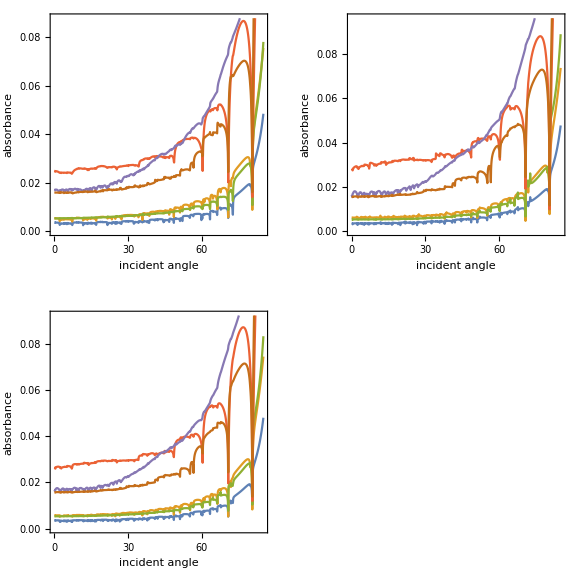
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

# Discussions for Key Question #2

There is no decisive difference about the results for linear chain and packed cluster configurations when the wavelength is varied, except in absorptance where packed cluster overall curve (excluding the oscillations) is different in shape from the others.

In incident angle variation, when the incident angle is larger than 40 degree, vertical linear chain reflectance, absorptance, transmittance, and absorbance are more steady than the others.

When the incident angle is varied, the reflectance decrease order is:
- horizontal linear chains
- vertical linear chains
- packed clusters

For incident angle less than 40 degree, the largest absorptance, the smallest transmittance, and the largest absorbance is in horizontal linear chains. For incident angle more than 40 degree, the largest absorptance, the smallest transmittance, and the largest absorbance is in vertical linear chains.

The reflectance, transmittance, and absorbance graphs do not share similar properties like the phase function, linear polarization degree, cross section efficiency, and asymmetry parameter graphs where linear chain’s curves have more similar shapes with bisphere’s and single sphere’s rather than packed cluster’s curves do. It is because reflectance, transmittance, and absorbance calculations bisect the system into up and down hemispheres. Hence, another factors in the system might come into play and have bigger influences to the extend that they would break the patterns we observe in the previous results.

# Concentration

## Target radius = 1.5 μm, thickness = 0.6 μm; sphere radius = 0.1 μm; results are the average of 200 random configurations

```mathematica
Grid[{{Style["Sphere number = 50","Chapter"], Style["Sphere number = 100","Chapter"],Style["Sphere number = 150","Chapter"]},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{,,}}]
```

Sphere number = 50 | Sphere number = 100 | Sphere number = 150
-Graphics3D- | -Graphics3D- | -Graphics3D-
 |  |

## Reflectance vs wavelength

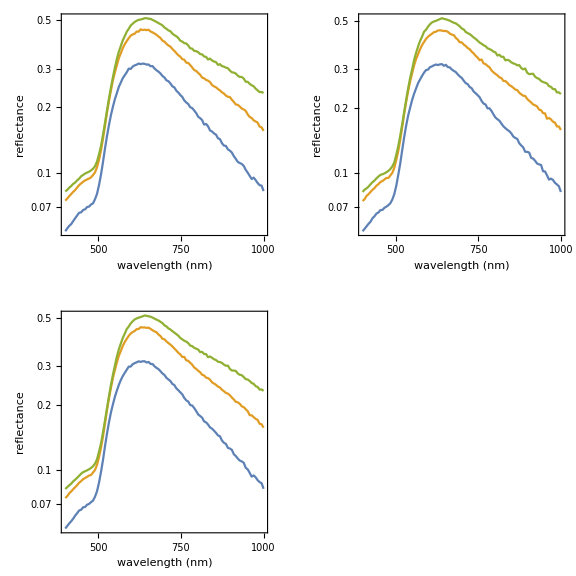
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorptance vs wavelength

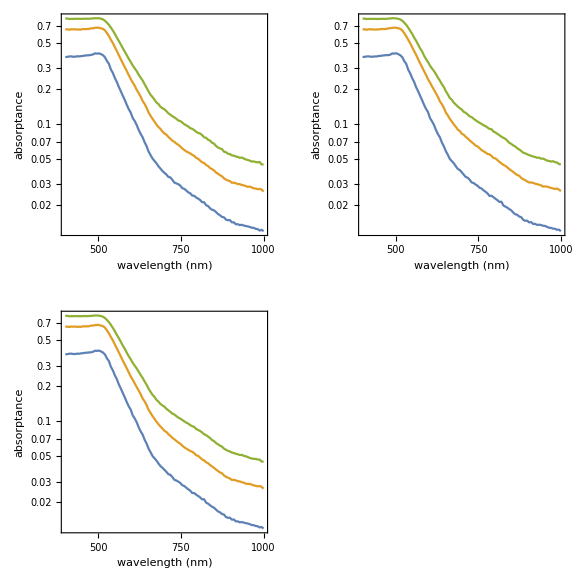
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Transmittance vs wavelength

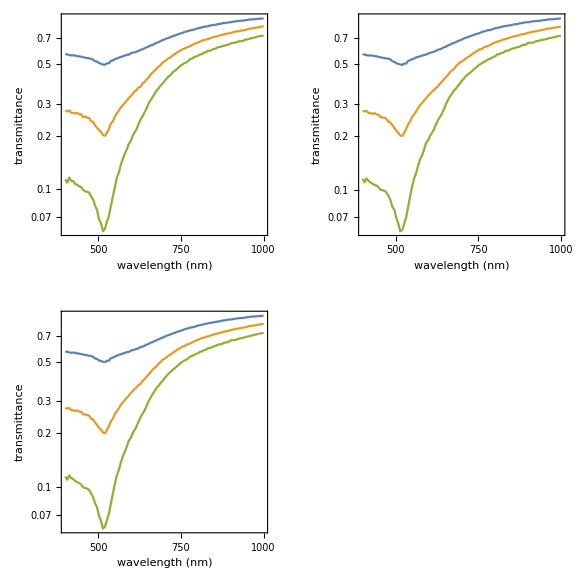
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorbance vs wavelength

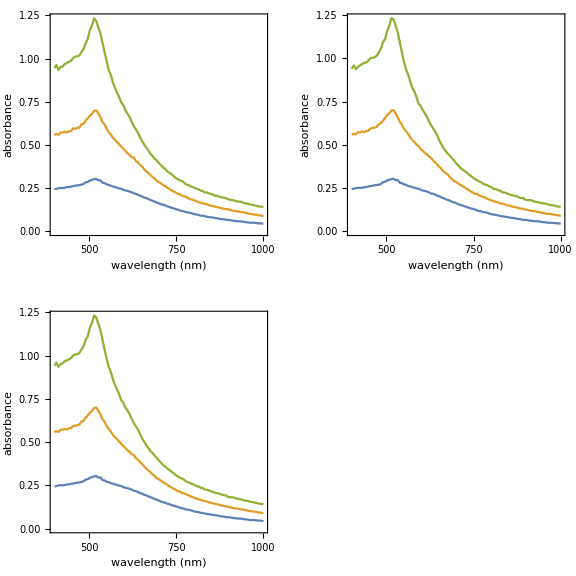
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

# Target Dimension

## Sphere number = 100, radius = 0.1 μm; results are the average of 200 random configurations

```mathematica
Grid[{{Style["Target radius = 1.3 μm, thickness = 0.8 μm","Chapter"],Style["Target radius = 1.5 μm, thickness = 0.6 μm","Chapter"],Style["Target radius = 2.0 μm, thickness = 0.3375 μm","Chapter"]},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{,,}}]
```

Target radius = 1.3 μm, thickness = 0.8 μm | Target radius = 1.5 μm, thickness = 0.6 μm | Target radius = 2.0 μm, thickness = 0.3375 μm
-Graphics3D- | -Graphics3D- | -Graphics3D-
 |  |

## Reflectance vs wavelength

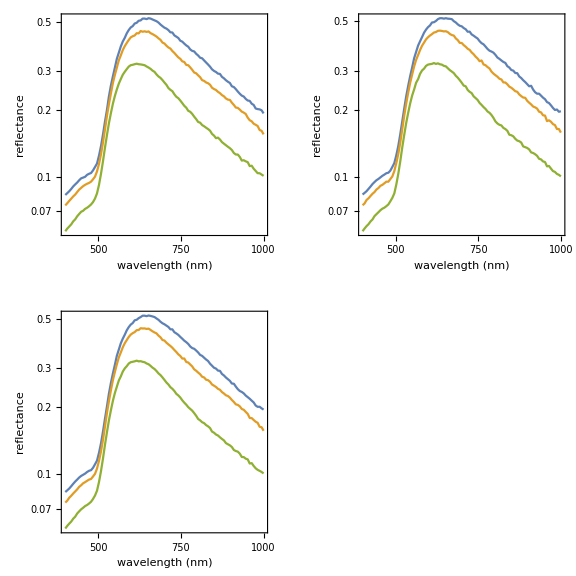
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorptance vs wavelength

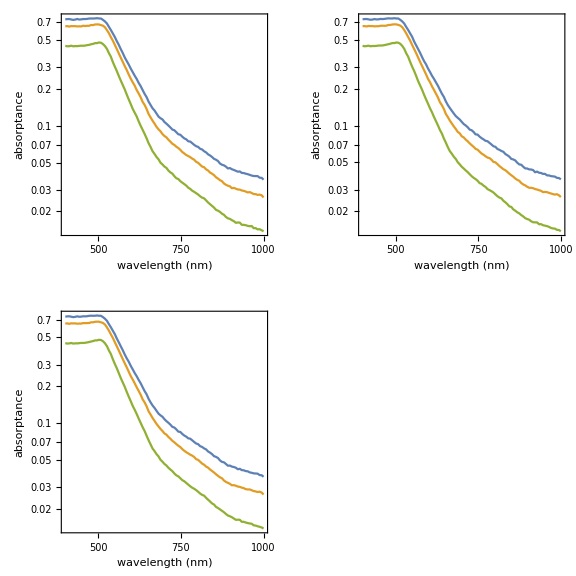
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Transmittance vs wavelength

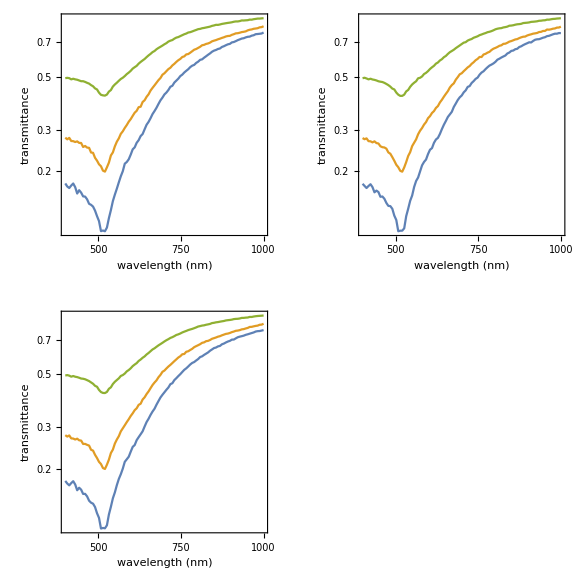
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorbance vs wavelength

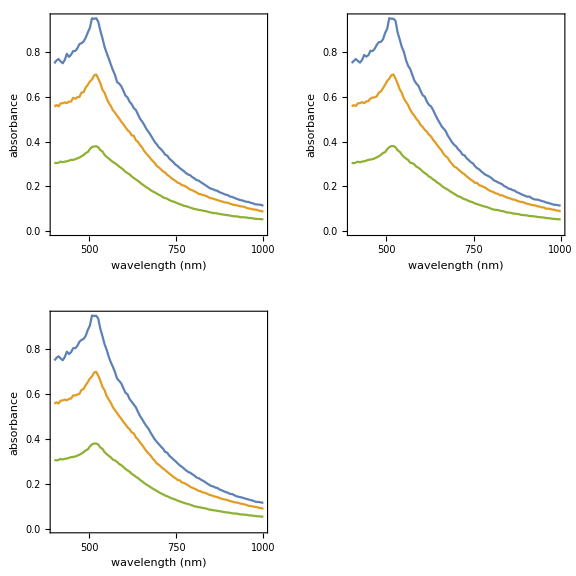
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

# Random Configuration

## Sphere number = 100, radius = 0.1 μm; target radius = 1.5 μm, thickness = 0.6 μm

```mathematica
Grid[{{Style["Configuration A","Chapter"],Style["Configuration B","Chapter"],Style["Configuration C","Chapter"]},
{-Graphics3D-,-Graphics3D-,-Graphics3D-},
{,,}}]
```

Configuration A | Configuration B | Configuration C
-Graphics3D- | -Graphics3D- | -Graphics3D-
 |  |

## Reflectance vs wavelength

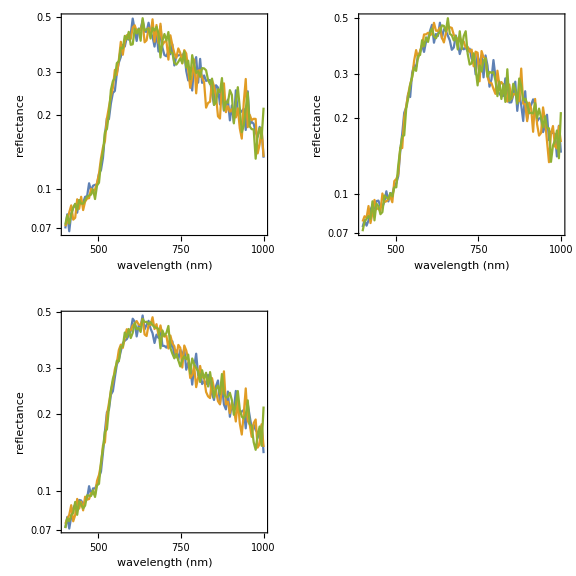
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorptance vs wavelength

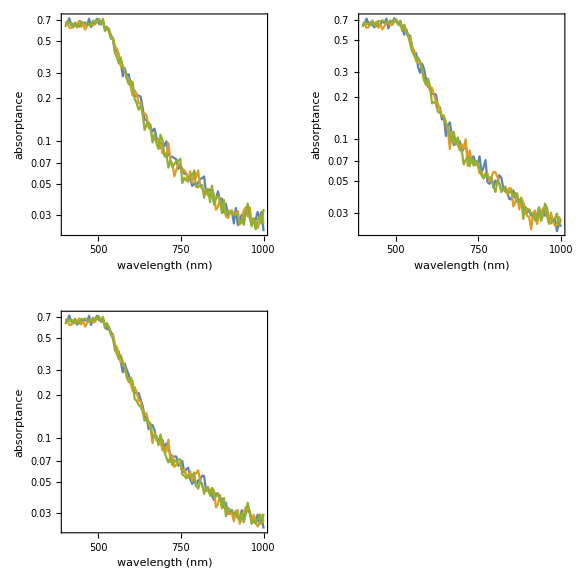
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Transmittance vs wavelength

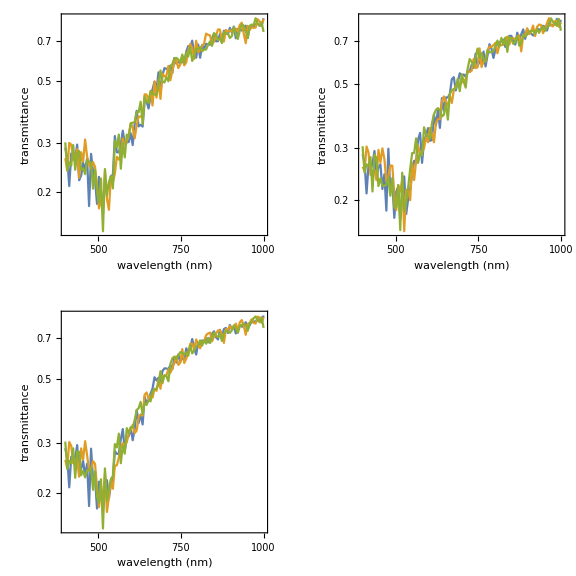
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorbance vs wavelength

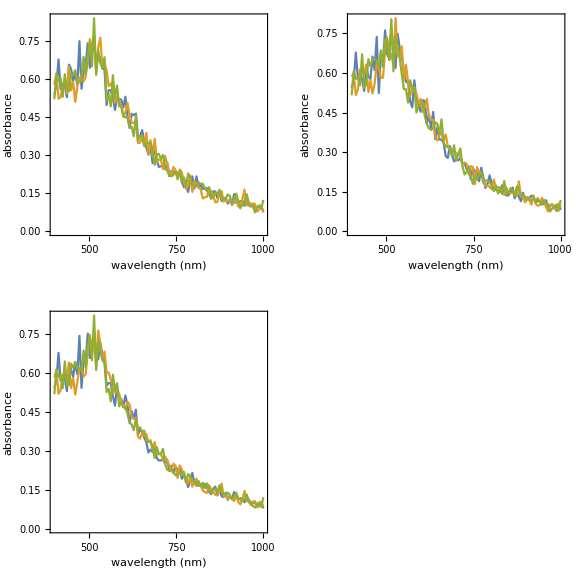
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Reflectance vs incident angle

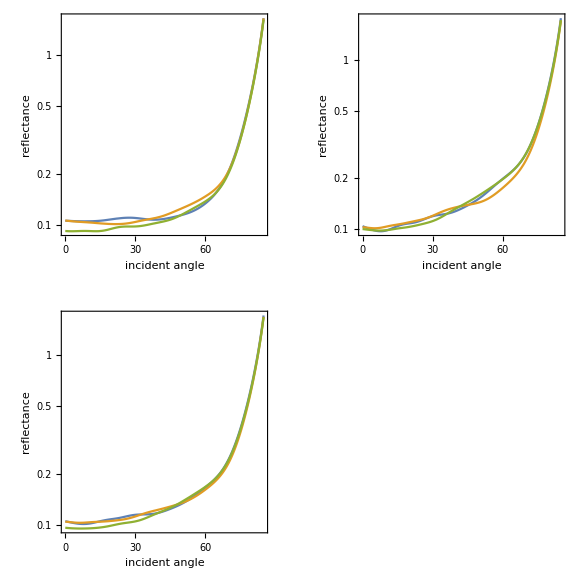
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorptance vs incident angle

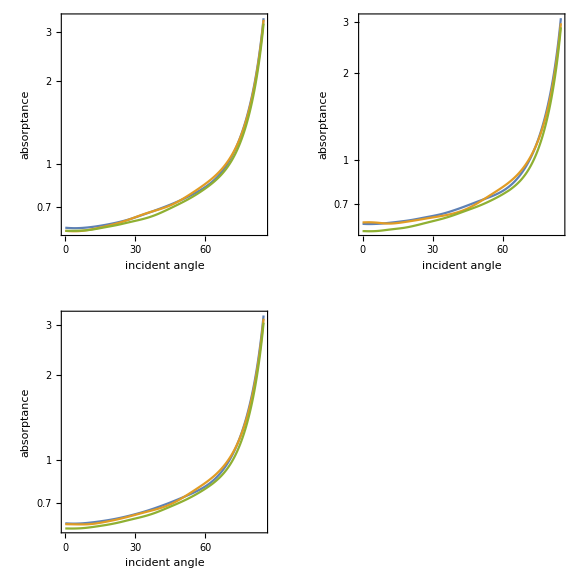
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Transmittance vs incident angle

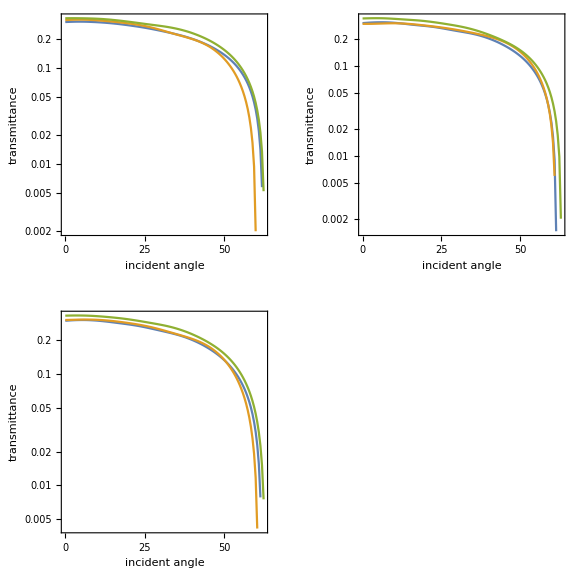
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorbance vs incident angle

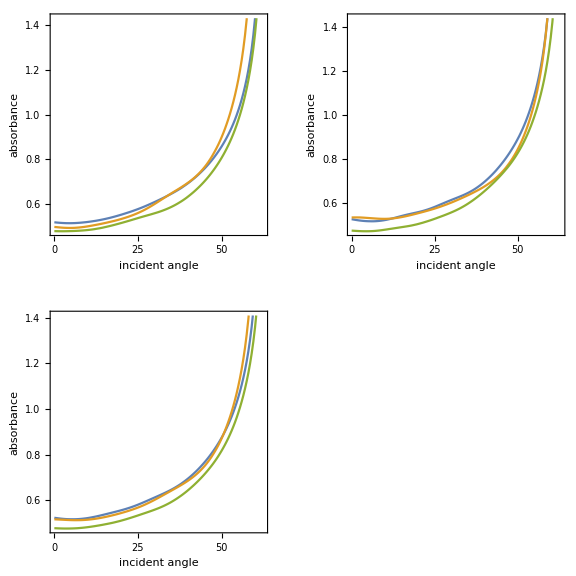
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

# Discussions

The reflectance, absorptance, and absorbance decrease order is:
- 150 spheres
- 100 spheres
- 50 spheres
The transmittance is the other way around

The reflectance, absorptance, and absorbance decrease order is:
- target radius = 1.3 um, thickness = 0.8 um
- target radius = 1.5 um, thickness = 0.6 um
- target radius = 2.0 um, thickness = 0.3375 um
The transmittance is the other way around

There are a lot of oscillations in the results for different target random configurations when the wavelength is varied. Hence, it is difficult to analyze the results.

There is a little difference in the results among the targets for different target random configurations when the incident angle is varied.

This result slightly deviate Beer-Lambert law, which states:

A=εℓ𝒸

where:
- A is the absorbance
- ε is the molar attenuation coefficient
- ℓ is the optical path length in cm
- 𝒸 is the concentration of the attenuating species,
because the random configuration targets have same molar attenuation coefficients, optical path lengths, and concentrations, but they do not have same absorbance (there is a little difference among them)

# Linear Chain and Packed Cluster Configurations Revisited

```mathematica
SetDirectory["C:\\Users\\hilma\\OneDrive\\Documents\\Post Project\\MSTM\\MSTM-main\\pre"];
config[file_]:=Module[{f,dat,tpos,trad,p},
f=OpenRead[file];
dat=ReadList[f, Table[Number, {4}]];
tpos=Table[dat[[i,{1,2,3}]],{i,Length[dat]}];
trad=Table[dat[[i,4]],{i,Length[dat]}];
p=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[dat]}];
p];
Grid[{{Style["Horizontal linear chains","Chapter"],Style["Vertical linear chains","Chapter"],Style["Packed clusters","Chapter"]},
{-Graphics3D-,-Graphics3D-,-Graphics3D-},{Graphics3D[config@"linear_chain_10_h_config.pos",Axes->True],Graphics3D[config@"linear_chain_10_v_config.pos",Axes->True],Graphics3D[config@"packed_cluster_10_config.pos",Axes->True]},
{"ℓ = 0.342 μm
𝒸 = 10/(3×3×0.342) spheres / μm^3
ℓ × 𝒸 = 10/(3×3) spheres / μm^2",
"ℓ = 1.93 μm
𝒸 = 10/(3×3×1.93) spheres / μm^3
ℓ × 𝒸 = 10/(3×3) spheres / μm^2",
"ℓ = 0.404 μm
𝒸 = 10/(3×3×0.404) spheres / μm^3
ℓ × 𝒸 = 10/(3×3) spheres / μm^2"}},Spacings->2]
```

Horizontal linear chains | Vertical linear chains | Packed clusters
-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-
ℓ = 0.342 μm
𝒸 = 10/(3×3×0.342) spheres / μm^3
ℓ × 𝒸 = 10/(3×3) spheres / μm^2 | ℓ = 1.93 μm
𝒸 = 10/(3×3×1.93) spheres / μm^3
ℓ × 𝒸 = 10/(3×3) spheres / μm^2 | ℓ = 0.404 μm
𝒸 = 10/(3×3×0.404) spheres / μm^3
ℓ × 𝒸 = 10/(3×3) spheres / μm^2

-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## How do we explain these results?

# Octant Types in Cuboid

-Graphics-

# Distinct Configuration (1/3)

## Sphere number = 100, radius = 0.1 μm; target shape = cuboid, dimension = 3.2 × 3 × 0.8 μm^3

```mathematica
Grid[{{Style["Configuration 1","Chapter"],Style["Configuration 2","Chapter"],Style["Configuration 3","Chapter"]},
{-Graphics3D-,-Graphics3D-,-Graphics3D-},
{,,},
{"Octant 1 sphere number = 13
Octant 2 sphere number = 12
Octant 3 sphere number = 13
Octant 4 sphere number = 12
Octant 5 sphere number = 13
Octant 6 sphere number = 11
Octant 7 sphere number = 14
Octant 8 sphere number = 12",
"Octant 1 sphere number = 20
Octant 2 sphere number = 18
Octant 3 sphere number = 22
Octant 4 sphere number = 20
Octant 5 sphere number = 6
Octant 6 sphere number = 5
Octant 7 sphere number = 5
Octant 8 sphere number = 4",
"Octant 1 sphere number = 6
Octant 2 sphere number = 5
Octant 3 sphere number = 5
Octant 4 sphere number = 4
Octant 5 sphere number = 20
Octant 6 sphere number = 18
Octant 7 sphere number = 22
Octant 8 sphere number = 20"}}]
```

Configuration 1 | Configuration 2 | Configuration 3
-Graphics3D- | -Graphics3D- | -Graphics3D-
 |  | 
Octant 1 sphere number = 13
Octant 2 sphere number = 12
Octant 3 sphere number = 13
Octant 4 sphere number = 12
Octant 5 sphere number = 13
Octant 6 sphere number = 11
Octant 7 sphere number = 14
Octant 8 sphere number = 12 | Octant 1 sphere number = 20
Octant 2 sphere number = 18
Octant 3 sphere number = 22
Octant 4 sphere number = 20
Octant 5 sphere number = 6
Octant 6 sphere number = 5
Octant 7 sphere number = 5
Octant 8 sphere number = 4 | Octant 1 sphere number = 6
Octant 2 sphere number = 5
Octant 3 sphere number = 5
Octant 4 sphere number = 4
Octant 5 sphere number = 20
Octant 6 sphere number = 18
Octant 7 sphere number = 22
Octant 8 sphere number = 20

# Distinct Configuration (2/3)

## Sphere number = 100, radius = 0.1 μm; target shape = cuboid, dimension = 3.2 × 3 × 0.8 μm^3

```mathematica
Grid[{{Style["Configuration 4","Chapter"],Style["Configuration 5","Chapter"],Style["Configuration 6","Chapter"]},
{-Graphics3D-,-Graphics3D-,-Graphics3D-},
{,,},
{"Octant 1 sphere number = 20
Octant 2 sphere number = 6
Octant 3 sphere number = 4
Octant 4 sphere number = 20
Octant 5 sphere number = 18
Octant 6 sphere number = 5
Octant 7 sphere number = 5
Octant 8 sphere number = 22",
"Octant 1 sphere number = 6
Octant 2 sphere number = 20
Octant 3 sphere number = 20
Octant 4 sphere number = 4
Octant 5 sphere number = 5
Octant 6 sphere number = 18
Octant 7 sphere number = 22
Octant 8 sphere number = 5",
"Octant 1 sphere number = 33
Octant 2 sphere number = 6
Octant 3 sphere number = 4
Octant 4 sphere number = 37
Octant 5 sphere number = 5
Octant 6 sphere number = 5
Octant 7 sphere number = 5
Octant 8 sphere number = 5"}}]
```

Configuration 4 | Configuration 5 | Configuration 6
-Graphics3D- | -Graphics3D- | -Graphics3D-
 |  | 
Octant 1 sphere number = 20
Octant 2 sphere number = 6
Octant 3 sphere number = 4
Octant 4 sphere number = 20
Octant 5 sphere number = 18
Octant 6 sphere number = 5
Octant 7 sphere number = 5
Octant 8 sphere number = 22 | Octant 1 sphere number = 6
Octant 2 sphere number = 20
Octant 3 sphere number = 20
Octant 4 sphere number = 4
Octant 5 sphere number = 5
Octant 6 sphere number = 18
Octant 7 sphere number = 22
Octant 8 sphere number = 5 | Octant 1 sphere number = 33
Octant 2 sphere number = 6
Octant 3 sphere number = 4
Octant 4 sphere number = 37
Octant 5 sphere number = 5
Octant 6 sphere number = 5
Octant 7 sphere number = 5
Octant 8 sphere number = 5

# Distinct Configuration (3/3)

## Sphere number = 100, radius = 0.1 μm; target shape = cuboid, dimension = 3.2 × 3 × 0.8 μm^3

```mathematica
Grid[{{Style["Configuration 7","Chapter"],Style["Configuration 8","Chapter"],Style["Configuration 9","Chapter"]},
{-Graphics3D-,-Graphics3D-,-Graphics3D-},
{,,},
{"Octant 1 sphere number = 6
Octant 2 sphere number = 33
Octant 3 sphere number = 37
Octant 4 sphere number = 4
Octant 5 sphere number = 5
Octant 6 sphere number = 5
Octant 7 sphere number = 5
Octant 8 sphere number = 5",
"Octant 1 sphere number = 6
Octant 2 sphere number = 5
Octant 3 sphere number = 5
Octant 4 sphere number = 4
Octant 5 sphere number = 33
Octant 6 sphere number = 5
Octant 7 sphere number = 5
Octant 8 sphere number = 37",
"Octant 1 sphere number = 6
Octant 2 sphere number = 5
Octant 3 sphere number = 5
Octant 4 sphere number = 4
Octant 5 sphere number = 5
Octant 6 sphere number = 33
Octant 7 sphere number = 37
Octant 8 sphere number = 5"}}]
```

Configuration 7 | Configuration 8 | Configuration 9
-Graphics3D- | -Graphics3D- | -Graphics3D-
 |  | 
Octant 1 sphere number = 6
Octant 2 sphere number = 33
Octant 3 sphere number = 37
Octant 4 sphere number = 4
Octant 5 sphere number = 5
Octant 6 sphere number = 5
Octant 7 sphere number = 5
Octant 8 sphere number = 5 | Octant 1 sphere number = 6
Octant 2 sphere number = 5
Octant 3 sphere number = 5
Octant 4 sphere number = 4
Octant 5 sphere number = 33
Octant 6 sphere number = 5
Octant 7 sphere number = 5
Octant 8 sphere number = 37 | Octant 1 sphere number = 6
Octant 2 sphere number = 5
Octant 3 sphere number = 5
Octant 4 sphere number = 4
Octant 5 sphere number = 5
Octant 6 sphere number = 33
Octant 7 sphere number = 37
Octant 8 sphere number = 5

## Reflectance vs wavelength

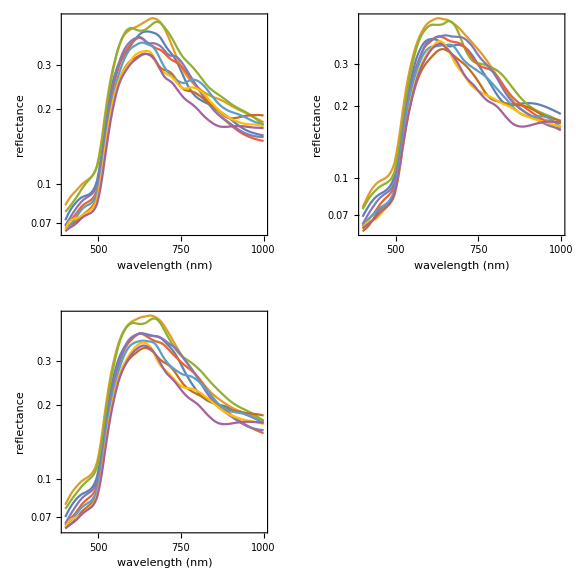
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorptance vs wavelength

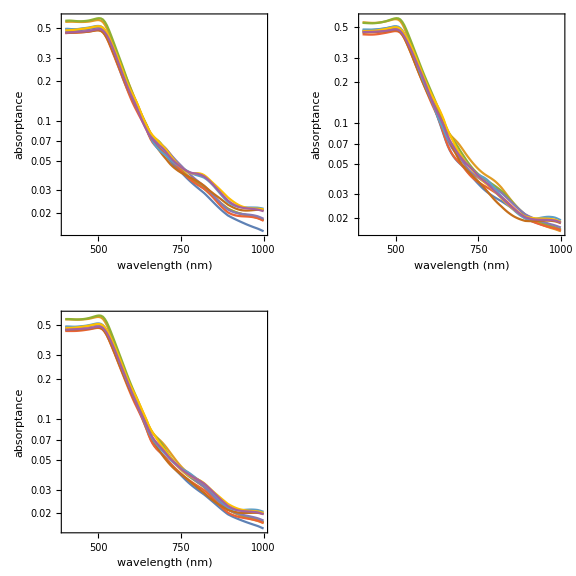
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Transmittance vs wavelength

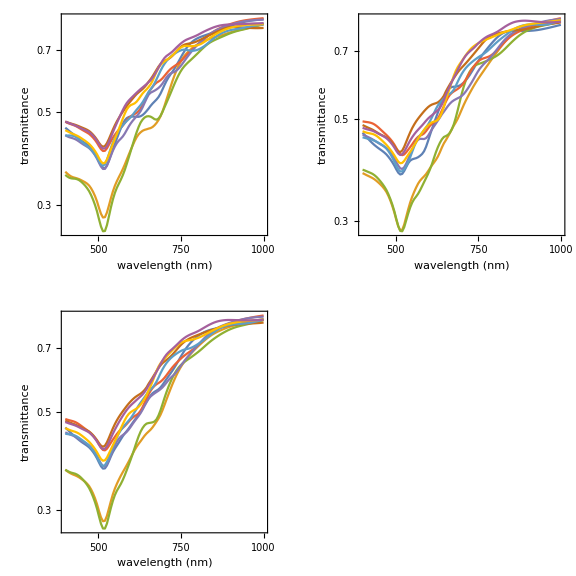
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorbance vs wavelength

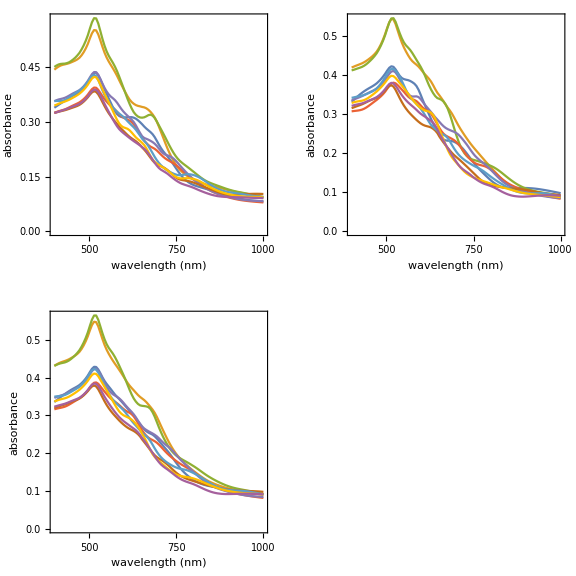
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Reflectance vs incident angle

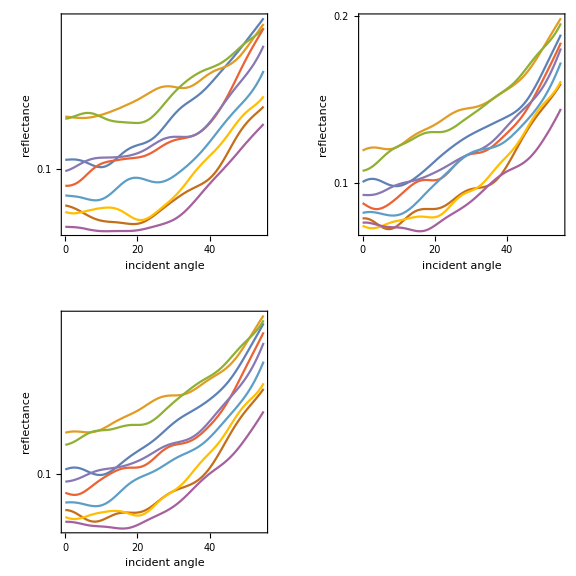
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorptance vs incident angle

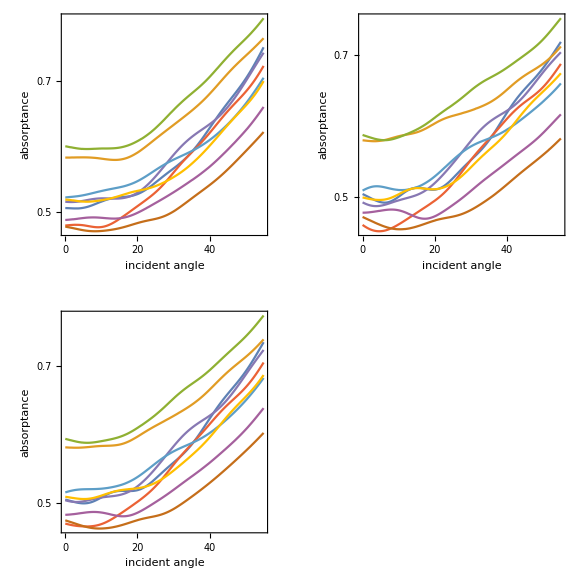
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Transmittance vs incident angle

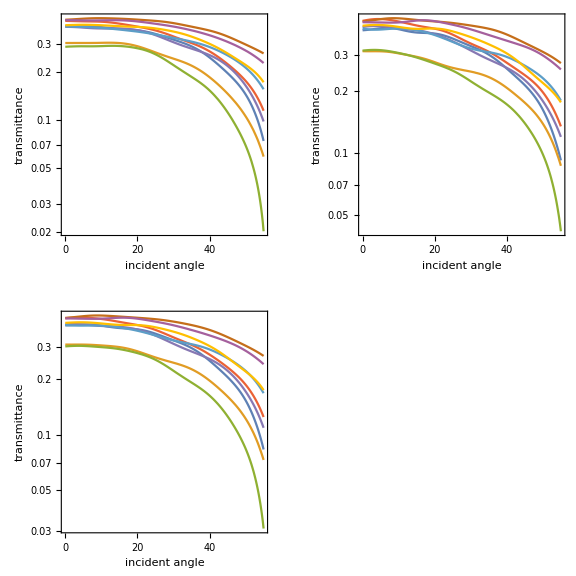
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

## Absorbance vs incident angle

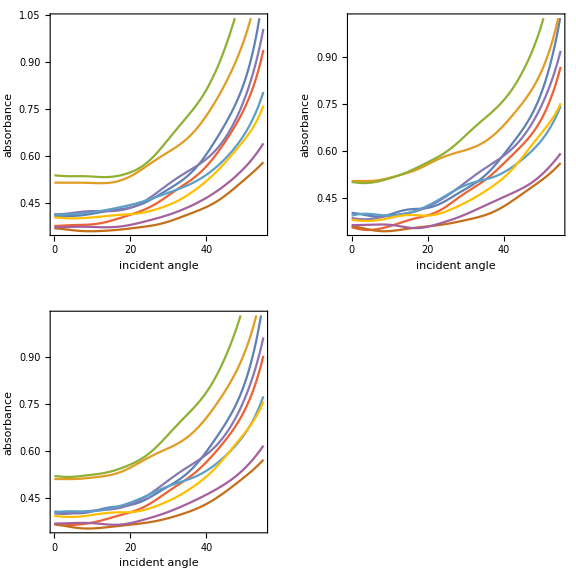
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

# Discussions for the Distinct Configuration Results

As before, the results plotted against wavelength are mostly indistinguishable. However, the transmittance and absorbance for Configuration 2 and Configuration 3 differ from the others.

The results could be distinguished clearly when they are plotted against incident angle:

Configuration 2 and 3 are categorized as Class A

Configuration 1, 4, and 5 are categorized as Class B

Configuration 7 and 8 are categorized as Class C

Configuration 6 and 9 are categorized as Class D

In this case, the reflectance, absorptance, and absorbance decrease order in general is:
- Class A
- Class B and C
- Class D
The transmittance is the other way around

The result average gradients for Class B are the largest

How do we explain these results?

# Hypothesis

## Top view:

```mathematica
SetDirectory["C:\\Users\\hilma\\OneDrive\\Documents\\Post Project\\MSTM\\MSTM-main\\pre"];
config[file_]:=Module[{f,dat,tpos,trad,p},
f=OpenRead[file];
dat=ReadList[f, Table[Number, {4}]];
tpos=Table[dat[[i,{1,2,3}]],{i,Length[dat]}];
trad=Table[dat[[i,4]],{i,Length[dat]}];
p=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[dat]}];
p];
Grid[{{Style["Class A:","Title"],Style["Configuration 2","Chapter"],Style["Configuration 3","Chapter"]},{"",Graphics3D[config["beer_2_config.pos"],ViewPoint->Above,ImageSize->Small],Graphics3D[config["beer_3_config.pos"],ViewPoint->Above,ImageSize->Small]},{Style["Class B:","Title"],Style["Configuration 1","Chapter"],Style["Configuration 4","Chapter"],Style["Configuration 5","Chapter"]},{"",Graphics3D[config["beer_1_config.pos"],ViewPoint->Above,ImageSize->Small],Graphics3D[config["beer_4_config.pos"],ViewPoint->Above,ImageSize->Small],Graphics3D[config["beer_5_config.pos"],ViewPoint->Above,ImageSize->Small]},{Style["Class C:","Title"],Style["Configuration 7","Chapter"],Style["Configuration 8","Chapter"]},{"",Graphics3D[config["beer_7_config.pos"],ViewPoint->Above,ImageSize->Small],Graphics3D[config["beer_8_config.pos"],ViewPoint->Above,ImageSize->Small]},{Style["Class D:","Title"],Style["Configuration 6","Chapter"],Style["Configuration 9","Chapter"]},{"",Graphics3D[config["beer_6_config.pos"],ViewPoint->Above,ImageSize->Small],Graphics3D[config["beer_9_config.pos"],ViewPoint->Above,ImageSize->Small]}}]
```

Class A: | Configuration 2 | Configuration 3 | 
 | -Graphics3D- | -Graphics3D- | 
Class B: | Configuration 1 | Configuration 4 | Configuration 5
 | -Graphics3D- | -Graphics3D- | -Graphics3D-
Class C: | Configuration 7 | Configuration 8 | 
 | -Graphics3D- | -Graphics3D- | 
Class D: | Configuration 6 | Configuration 9 | 
 | -Graphics3D- | -Graphics3D- |

# Approach #1

## Top view:

```mathematica
apercent={22.52616538004751,26.817577828397877,23.80646306818182,22.483320932539684,24.059949221716025,24.52763310185185,25.726011839207047,23.135074943438916,22.07447193287037};
Grid[{{Style["Class A:","Title"],Style["Configuration 2","Chapter"],Style["Configuration 3","Chapter"]},{"",-Graphics-,-Graphics-},{Style["Area coverage (%) = ","Subtitle"],apercent[[2]],apercent[[3]]},{Style["Class B:","Title"],Style["Configuration 1","Chapter"],Style["Configuration 4","Chapter"],Style["Configuration 5","Chapter"]},{"",-Graphics-,-Graphics-,-Graphics-},{Style["Area coverage (%) = ","Subtitle"],apercent[[1]],apercent[[4]],apercent[[5]]},
{Style["Class C:","Title"],Style["Configuration 7","Chapter"],Style["Configuration 8","Chapter"]},{"",-Graphics-,-Graphics-},{Style["Area coverage (%) = ","Subtitle"],apercent[[7]],apercent[[8]]},{Style["Class D:","Title"],Style["Configuration 6","Chapter"],Style["Configuration 9","Chapter"]},{"",-Graphics-,-Graphics-},{Style["Area coverage (%) = ","Subtitle"],apercent[[6]],apercent[[9]]}}]
```

Class A: | Configuration 2 | Configuration 3 | 
 | -Graphics- | -Graphics- | 
Area coverage (%) =  | 26.8176 | 23.8065 | 
Class B: | Configuration 1 | Configuration 4 | Configuration 5
 | -Graphics- | -Graphics- | -Graphics-
Area coverage (%) =  | 22.5262 | 22.4833 | 24.0599
Class C: | Configuration 7 | Configuration 8 | 
 | -Graphics- | -Graphics- | 
Area coverage (%) =  | 25.726 | 23.1351 | 
Class D: | Configuration 6 | Configuration 9 | 
 | -Graphics- | -Graphics- | 
Area coverage (%) =  | 24.5276 | 22.0745 |

# Approach #2

## Top view:

```mathematica
anum={61,62,65,47,51,45,55,48,50};
Grid[{{Style["Class A:","Title"],Style["Configuration 2","Chapter"],Style["Configuration 3","Chapter"]},{"",-Graphics-,-Graphics-},{Style["Aggregate number = ","Subtitle"],anum[[2]],anum[[3]]},{Style["Class B:","Title"],Style["Configuration 1","Chapter"],Style["Configuration 4","Chapter"],Style["Configuration 5","Chapter"]},{"",-Graphics-,-Graphics-,-Graphics-},{Style["Aggregate number = ","Subtitle"],anum[[1]],anum[[4]],anum[[5]]},
{Style["Class C:","Title"],Style["Configuration 7","Chapter"],Style["Configuration 8","Chapter"]},{"",-Graphics-,-Graphics-},{Style["Aggregate number = ","Subtitle"],anum[[7]],anum[[8]]},{Style["Class D:","Title"],Style["Configuration 6","Chapter"],Style["Configuration 9","Chapter"]},{"",-Graphics-,-Graphics-},{Style["Aggregate number = ","Subtitle"],anum[[6]],anum[[9]]}}]
```

Class A: | Configuration 2 | Configuration 3 | 
 | -Graphics- | -Graphics- | 
Aggregate number =  | 62 | 65 | 
Class B: | Configuration 1 | Configuration 4 | Configuration 5
 | -Graphics- | -Graphics- | -Graphics-
Aggregate number =  | 61 | 47 | 51
Class C: | Configuration 7 | Configuration 8 | 
 | -Graphics- | -Graphics- | 
Aggregate number =  | 55 | 48 | 
Class D: | Configuration 6 | Configuration 9 | 
 | -Graphics- | -Graphics- | 
Aggregate number =  | 45 | 50 |

# Side View Analysis

```mathematica
apercent={35.49307839912281,32.37847222222223,32.007728494623656,30.615591397849464,39.219926075268816,27.692169540229884,33.58800287356322,26.42798013245033,34.139072847682115};
anum={6,15,15,8,9,11,10,11,10};
Grid[{{Style["Class A:","Title"],Style["Configuration 2","Chapter"],Style["Configuration 3","Chapter"]},{"",-Graphics-,-Graphics-},

{Style["Area coverage (%) = ","Subtitle"],apercent[[2]],apercent[[3]]},{Style["Aggregate number = ","Subtitle"],anum[[2]],anum[[3]]},{Style["Class B:","Title"],Style["Configuration 1","Chapter"],Style["Configuration 4","Chapter"],Style["Configuration 5","Chapter"]},{"",-Graphics-,-Graphics-,-Graphics-},
{Style["Area coverage (%) = ","Subtitle"],apercent[[1]],apercent[[4]],apercent[[5]]},{Style["Aggregate number = ","Subtitle"],anum[[1]],anum[[4]],anum[[5]]},
{Style["Class C:","Title"],Style["Configuration 7","Chapter"],Style["Configuration 8","Chapter"]},{"",-Graphics-,-Graphics-},
{Style["Area coverage (%) = ","Subtitle"],apercent[[7]],apercent[[8]]},{Style["Aggregate number = ","Subtitle"],anum[[7]],anum[[8]]},{Style["Class D:","Title"],Style["Configuration 6","Chapter"],Style["Configuration 9","Chapter"]},{"",-Graphics-,-Graphics-},
{Style["Area coverage (%) = ","Subtitle"],apercent[[6]],apercent[[9]]},{Style["Aggregate number = ","Subtitle"],anum[[6]],anum[[9]]}},Spacings->2]
```

Class A: | Configuration 2 | Configuration 3 | 
 | -Graphics- | -Graphics- | 
Area coverage (%) =  | 32.3785 | 32.0077 | 
Aggregate number =  | 15 | 15 | 
Class B: | Configuration 1 | Configuration 4 | Configuration 5
 | -Graphics- | -Graphics- | -Graphics-
Area coverage (%) =  | 35.4931 | 30.6156 | 39.2199
Aggregate number =  | 6 | 8 | 9
Class C: | Configuration 7 | Configuration 8 | 
 | -Graphics- | -Graphics- | 
Area coverage (%) =  | 33.588 | 26.428 | 
Aggregate number =  | 10 | 11 | 
Class D: | Configuration 6 | Configuration 9 | 
 | -Graphics- | -Graphics- | 
Area coverage (%) =  | 27.6922 | 34.1391 | 
Aggregate number =  | 11 | 10 |

# Random Configurations Revisited

## Top view:

```mathematica
apercent={28.71697869744745,28.65950948212983,27.680049668874172};
anum={41,42,44};
Grid[{{"",Style["Configuration A", "Chapter"],Style["Configuration B", "Chapter"],Style["Configuration C", "Chapter"]},
{"",-Graphics-,-Graphics-,-Graphics-},
{Style["Area coverage (%) = ","Subtitle"], apercent[[1]],apercent[[2]],apercent[[3]]}, 
{Style["Aggregate number = ","Subtitle"], anum[[1]],anum[[2]],anum[[3]]}},Spacings->2]
```

| Configuration A | Configuration B | Configuration C
 | -Graphics- | -Graphics- | -Graphics-
Area coverage (%) =  | 28.717 | 28.6595 | 27.68
Aggregate number =  | 41 | 42 | 44

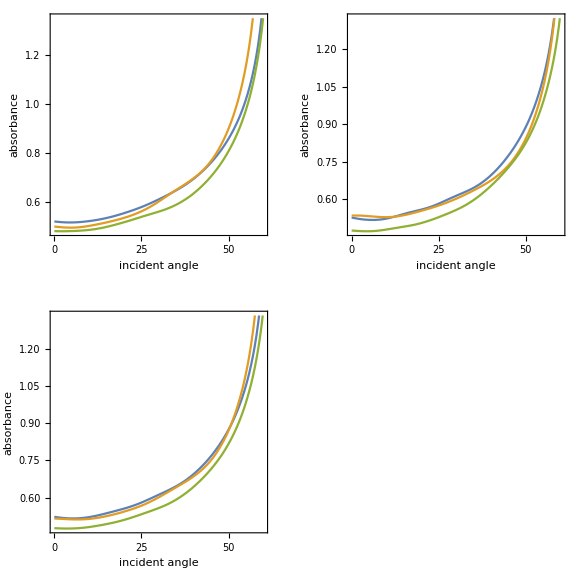
-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

# Linear Chain and Packed Cluster Configurations Revisited, Again

## Top view:

```mathematica
apercent={4.725257640369581,2.259765625,3.9321801391862956};
anum={6,1,1};
Grid[{{"", Style["Horizontal Linear Chains", "Chapter"], Style["Vertical Linear Chains", "Chapter"], Style["Packed Clusters", "Chapter"]},
  {"",-Graphics-,-Graphics-,-Graphics-},
  {Style["Area coverage (%) = ", "Subtitle"], apercent[[1]],apercent[[2]], apercent[[3]]}, 
  {Style["Aggregate number = ", "Subtitle"], anum[[1]], anum[[2]],anum[[3]]}}, Spacings -> 2]
```

| Horizontal Linear Chains | Vertical Linear Chains | Packed Clusters
 | -Graphics- | -Graphics- | -Graphics-
Area coverage (%) =  | 4.72526 | 2.25977 | 3.93218
Aggregate number =  | 6 | 1 | 1

## Side view:

```mathematica
apercent={2.817556634304207,4.580622371188222,3.348250404530744};
anum={1,6,1};
Grid[{{"", Style["Horizontal Linear Chains", "Chapter"], Style["Vertical Linear Chains", "Chapter"], Style["Packed Clusters", "Chapter"]},
  {"",-Graphics-,-Graphics-,-Graphics-},
  {Style["Area coverage (%) = ", "Subtitle"], apercent[[1]],apercent[[2]], apercent[[3]]}, 
  {Style["Aggregate number = ", "Subtitle"], anum[[1]], anum[[2]],anum[[3]]}}, Spacings -> 2]
```

| Horizontal Linear Chains | Vertical Linear Chains | Packed Clusters
 | -Graphics- | -Graphics- | -Graphics-
Area coverage (%) =  | 2.81756 | 4.58062 | 3.34825
Aggregate number =  | 1 | 6 | 1

-Graphics-
top left to right: E_(||), E_⊥
bottom left: unpolarized incident EM

# Summary

For phase functions and linear polarization degrees which are plotted against scattering angle, linear chain’s functions are more identical to bisphere’s and single sphere’s in both shapes and values rather than packed cluster’s functions.

For cross section efficiencies and asymmetry parameters which are plotted against wavelength, linear chain’s curves have more similar shapes with bisphere’s and single sphere’s rather than packed cluster’s curves do because packed cluster’s functions are wavier than the others.

We can conclude that linear chain aggregates have closer phase functions, linear polarization degrees, cross section efficiencies and asymmetry parameters to bispheres and single spheres than densely packed clusters do.

Hypothetically, it is because in linear chain aggregates there are less multiple scattering occurrence as the particles are less in contact with each other than the particles in packed clusters

We can also conclude that the optical characteristic difference strongly depends on angular distributions, instead of wavelength or refractive index.

In addition, aggregate configurations have greater influence on optical characteristics than particle numbers do, which is characterized by the same aggregate configuration’s functions with different sphere numbers having closer values to each other rather than the same sphere number configuration’s function with different aggregate configurations.

There is no decisive difference about the reflectance, transmittance, and absorbance for linear chain and packed cluster configurations when the wavelength is varied, except in absorptance where packed cluster overall curve (excluding the oscillations) is different in shape from the others.

The reflectance, transmittance, and absorbance graphs do not share similar properties like the phase function, linear polarization degree, cross section efficiency, and asymmetry parameter graphs where linear chain’s curves have more similar shapes with bisphere’s and single sphere’s rather than packed cluster’s curves do. It is because reflectance, transmittance, and absorbance calculations bisect the field directions into up and down hemispheres. Hence, another factors in the system might come into play and have bigger influences to the extend that they would break the patterns we observe in the previous results.

These another factors include target concentrations, optical path length (target thickness), and particle placements in the system

The reflectance, absorptance, and absorbance increase as the concentrations increase, the transmittance is the other way around

The reflectance, absorptance, and absorbance increase as the optical path length (target thickness) increase, the transmittance is the other way around

Particle placements in the system are also ones of the important factors because the simulation results show that different random placement configurations with the same kind of particles, target concentrations, and target thickness still yield different reflectance, absorptance, transmittance, and absorbance, hence deviating the Beer-Lambert law

By using distinct configurations based on octant partitioning, we observe that reflectance, absorptance, transmittance, and absorbance for small incident angle depend on the 2D gaps among the particles viewed from the detector (above). In our simulations, the 2D gaps are analyzed by using the approaches of 2D particle area coverage and aggregate number viewed from the above. The results show that reflectance, absorptance, and absorbance are in inverse proportion to the wide of the 2D particle gaps viewed from the above.

In incident angle variation, the reflectance, absorptance, and absorbance curve gradients are also in inverse proportion to the wide of the 2D particle gaps viewed from the side of the target. The transmittance is the other way around.